```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<Superradiance`SWSH`
```

```mathematica
<<MaTeX`
```

```mathematica
Clear[ParseTexPi,NullMap,IntParse];
ParseTexPi=(MaTeX@StringReplace[(ToString[#,InputForm]&)/@#1,{"Pi"->"\\pi","("|")"|"*"->"","-"->"\\text{-}"}]&);
NullMap=Map[(Null&)];
IntParse=Map[If[#==IntegerPart[#],IntegerPart[#],#]&];
```

```mathematica
Clear[frameticks];
frameticks[min_?NumericQ,max_?NumericQ,ss_?NumericQ,bs_?NumericQ,f_:Identity]:=frameticks[min,max,{ss,0.007,Gray},{bs,0.015,Gray},f];
frameticks[min_?NumericQ,max_?NumericQ,{ss_?NumericQ,st_?NumberQ},{bs_?NumericQ,bt_?NumberQ},f_:Identity]:=frameticks[min,max,{ss,st,Gray},{bs,bt,Gray},f];
frameticks[min_?NumericQ,max_?NumericQ,{ss_?NumericQ,st_?NumberQ,sc_?ColorQ},{bs_?NumericQ,bt_?NumberQ,bc_?ColorQ},f_:Identity]:=Join[
Table[If[Mod[i,bs]!=0,{i,Null,{st,0},sc},Nothing],{i,min,max,ss}],{#1,f[#2],##3}ᵀ&@@
Transpose@Table[{i,i,{bt,0},bc},{i,min,max,bs}]
];
```

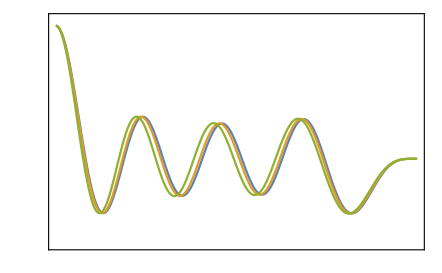

```mathematica
With[{S=SpinWeightedSpheroidalHarmonicS[-2,9,2,#]},Table[{xθ π,S[xθ π,0]},{xθ,0.,1.,0.001}]]&/@{0,0.999999*0.997,3.0}//ListPlot[#,Joined->True,Frame->True,PlotRange-> {{0,π},{-0.8,1.3}},FrameTicks->{{frameticks[-3,3,6/100,6/20,ParseTexPi@*IntParse@*N],frameticks[-3,3,6/100,6/20,NullMap]},{frameticks[0,π,π/48,π/6,ParseTexPi],frameticks[0,π,π/48,π/6,NullMap]}}]&
```

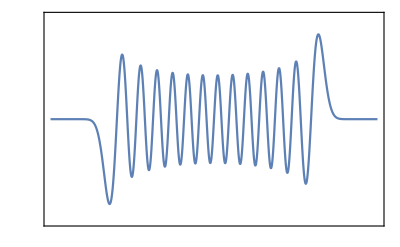

```mathematica
Plot[SphericalHarmonicY[50,25,θ,0],{θ,0,π},Frame->True,PlotRange-> {{0,π},0.8{-1,1}},FrameTicks->{{frameticks[-1,1,2/50,2/10,ParseTexPi@*IntParse@*N],frameticks[-1.,1.,0.05,0.2,NullMap]},{frameticks[0,π,π/48,π/6,ParseTexPi],frameticks[0,π,π/48,π/6,NullMap]}},PlotRangePadding->None]
```

```mathematica
data=Import["Data/phaseDelta_s-1_j07_w03.csv"]
```

{{0.7,-1,1,-1,0.3,0.701499,0.587903},{0.7,-1,1,0,0.3,0.828737,0.530781},{0.7,-1,1,1,0.3,0.895666,0.447493},{0.7,-1,2,-2,0.3,0.993609,-0.111699},{0.7,-1,2,-1,0.3,0.990835,-0.13491},2591,{0.7,-1,50,47,0.3,-0.795099,-0.606635},{0.7,-1,50,48,0.3,-0.79512,-0.606608},{0.7,-1,50,49,0.3,-0.79514,-0.606581},{0.7,-1,50,50,0.3,-0.795161,-0.606554}}
 |  |  |  |

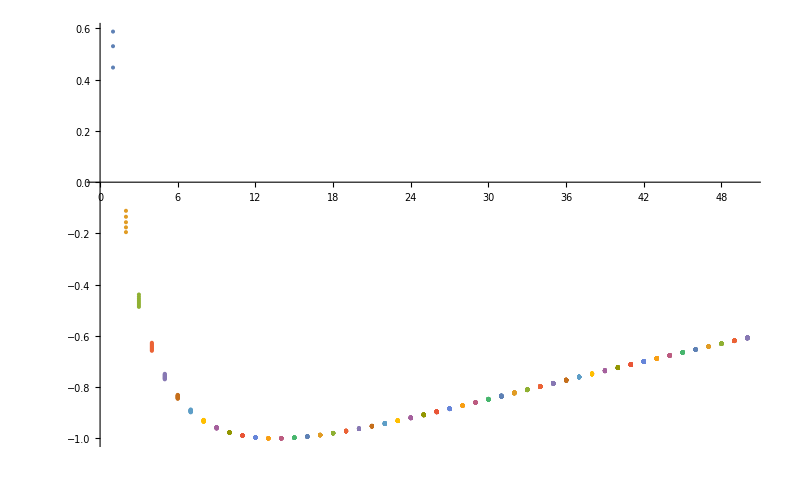

```mathematica
KeyValueMap[{ConstantArray[#1,Length[#2]],#2}ᵀ&]@GroupBy[data,(#1⟦3⟧&)->(#1⟦7⟧&)]//ListPlot[#,PlotRange->All]&
```

```mathematica
KeyValueMap[{#1,(Max[#2]/Min[#2])^Sign[Max[#2]]}&]@GroupBy[data,(#1⟦3⟧&)->(#1⟦6⟧&)]
```

{{1,1.27679},{2,1.01306},{3,1.02882},{4,1.03487},{5,1.03901},{6,1.04311},{7,1.04806},{8,1.05475},{9,1.06453},{10,1.08021},{11,1.10922},{12,1.17994},{13,1.6001},{14,1.65834},{15,1.16666},{16,1.09278},{17,1.06308},{18,1.04711},{19,1.03717},{20,1.03041},{21,1.02553},{22,1.02185},{23,1.01899},{24,1.0167},{25,1.01483},{26,1.01328},{27,1.01198},{28,1.01087},{29,1.00991},{30,1.00908},{31,1.00835},{32,1.00771},{33,1.00714},{34,1.00664},{35,1.00618},{36,1.00577},{37,1.0054},{38,1.00507},{39,1.00476},{40,1.00448},{41,1.00422},{42,1.00398},{43,1.00376},{44,1.00356},{45,1.00337},{46,1.0032},{47,1.00304},{48,1.00289},{49,1.00274},{50,1.00261}}